```mathematica
(* things to implement and modify in the code;

6. Poisson process for death;
1. first order reactions such as disassociation of receptor/ligand: prob = 1 - Exp(-k δt);

5. check for whether the particle actually crossed the cell boundary;
7. does the order of zeroth, first and second order matter in code execution?
*)
```

### determining the unbinding and binding radius

```mathematica
{bindrad,unbindrad}=NotebookEvaluate["C:\\Users\\Ali Hashmi\\Desktop\\research\\brownian simulation of nodal lefty\\current version\\binding-unbinding radius.nb"][[1;;2]];
```

### creating regions and constraints

```mathematica
ℛ = ImplicitRegion[x^2 + y^2 ≤ 0.25^2,{x,y}]; (* defining the region containing the molecules in a single cell *)
```

```mathematica
(* creating necessary regions and constraints *)
Subscript[ℛ, 2]=ImplicitRegion[x^2+y^2≤0.75^2,{x,y}]; (* creating the circular cell *)
Subscript[ℛ, 2b]=ImplicitRegion[x^2+y^2==0.75^2,{x,y}];
Subscript[ℛ, 3]=BoundaryMeshRegion[{{-1,-1},{1,-1},{1,1},{-1,1}},Line[{1,2,3,4,1}]];
(* creating the bounding box *)
```

### functions to create intial particle configuration

```mathematica
(* setting up initial configuration of ligands *)
initialParticleConfig[name_String,{x_?NumberQ,y_?NumberQ},number_?IntegerQ]:= Module[{specie, specieBoundaryIndex, speciePts},
specie = RandomReal[{x,y},{number,2}]; (* this creates a number of particles for specified domains *)
specie= Select[specie,#∈ℛ&]; (* select those particles that are present within the cell *)
specie = Association@MapIndexed[First@#2-> #1&,Thread[{name,specie}]]; (* lets thread the particles with a rule where the particles are associated with an index, their name and their coordinates *)

specieBoundaryIndex = (#[[2]]∈ℛ)&/@Values[specie]/.{True-> 0,False->1}; (* a mapping over particle position to check whether the particles are outside the defined boundaries (cells) or within it. a particle inside would yield True (replace True with 0) and external to the region will yield False (replace with 1) *)
specieBoundaryIndex = Association@Thread[Range[Length@specie]-> specieBoundaryIndex]; (* putting an index to the previous result for unique identification of particle *)

speciePts = Values@specie[[All,2]]; (* this will only extract the particle positions *)

Return@{specie,specieBoundaryIndex,speciePts};(* now i can return three variables. specie (<| particle number -> {{"Nodal || Lefty"},{x,y}} ... |> ), specieBoundaryIndex (<| particle number -> 1 || 0 ... |>) and speciePts {{x,y}....} *)
];

(* setting up configuration of membrane proteins *)
membraneReceptorConfig[{x_?NumberQ,y_?NumberQ},radius_?NumberQ,number_?IntegerQ]:= Module[{membranePts,membraneIndex},
(* this creates a random number of particle on a circle, basically representing membrane proteins *)
membranePts =Table[RandomPoint[Circle[{x,y},radius]],number]; 
membraneIndex = Thread[Range[number]-> Thread[{membranePts,0,None,"type"}]]; (* putting an identification number for the previous result i.e. receptor number -> {coord, 0 or 1, BoundTo/None, Type-Ligand} *)
Return@{membranePts,membraneIndex} ;(* returns membranePts ({x,y}....) and membraneIndex (membrane protein number -> {x,y},0,None,Type) *);
];
```

### helper functions

#### brownian walk (free ligands)

```mathematica
BrownianWalk[number_,elem_]:= Module[{oldposition=elem[[2]],newposition,step,tag=elem[[1]]},
step = {RandomVariate[NormalDistribution[0,0.01]],RandomVariate[NormalDistribution[0,0.01]]}; (* take a random number from a Gaussian where the width can be defined as Sqrt[2 Subscript[D, coeff] δt] *)
newposition =oldposition +step; (* add the new step to the original particle position *)
number-> {tag,newposition} (* thread the particle with its type and new position *)
]
```

```mathematica
BrownianFunc[assoc_]:= Module[{temp},
temp=Association[KeyValueMap[BrownianWalk,assoc]]
]
```

#### brownian walk (for receptors)

```mathematica
(* strategy: get all the membrane pts. rotate them using a random number (angle) generated from a Gaussain function. export updated membrane pts out of the module *)
BrownianWalkMembrane[receptorpos_,membraneind_]:= Module[{membranepos,membrane,angle, center},
center = {0,0};
angle =π/1800.; (* 0.1 degree rotation about center {0,0} *)
membranepos=RotationTransform[RandomVariate[NormalDistribution[0,angle]],center][#]&/@receptorpos; (* here we generate the new position *)
membrane = Table[i->{membranepos[[i]],Sequence@@membraneind[[i,2,2;;]]},{i,1,Length@membraneind}]; (* updating the position in the membraneindex *)
{membranepos,membrane} (* exporting the membrane position and the updated membraneindex *)
]/;Length@membraneind>0
```

#### ballistic reflection

```mathematica
ballisticReflect[inside_]:= Module[{near},
near = RegionNearest[Subscript[ℛ, 2b],inside];
inside+2*(near-inside)
] (* region specification should be a boundary *)
```

#### periodic boundaries for diffusion

```mathematica
periodicBoundary[finalpt_]:= Module[{x,y},
{x,y}=finalpt;
Which[x≥1,x=x-2,x≤-1,x=2+x,True,x];
Which[y≥1,y=y-2,y≤-1,y=2+y,True,y];
{x,y}
] (* box dimension is 2 *)
```

#### ligand spatial check

```mathematica
ligandCheck[particles_,particleBoundaryIndex_]:= Module[{specie = particles,speciekeys,coordsspecie,
indexspecie,threadList},

speciekeys = Keys@specie; (* the indices of the particles *)
coordsspecie = Values@specie[[All,2]]; (* the positions of the particles *)
indexspecie = Values@particleBoundaryIndex;  (* whether particles are present inside 0 or outside the cells 1 *)
threadList = Thread[{speciekeys,indexspecie,coordsspecie}]; (* lets thread the above three together *)

(* update a particle that was inside but takes a step outside *)
threadList = threadList/.{ind_?IntegerQ,x_?IntegerQ,y_List}/;x==0 &&!y∈Subscript[ℛ, 2]:> {ind,1,y};
(* prevent particles that are outside to step inside *)  
threadList = threadList/.{ind_?IntegerQ,x_?IntegerQ,y_List}/;x==1&&y∈Subscript[ℛ, 2]:> {ind,1,ballisticReflect[y]};
(* apply periodic boundary condition at the edges *)
threadList = threadList/.{ind_?IntegerQ,x_?IntegerQ,y_List}/;x==1&&!y∈Subscript[ℛ, 3]:> {ind,1,periodicBoundary[y]}; 

threadList (* final check goes outside the module without using Return *)
]
```

#### ligand-receptor interaction

```mathematica
nearestFunction[ligandList_, membraneIndex_,membranepts_]:= With[{bindrad = 0.01},
Module[{freeReceptors,receptormap,interactions,ligandlist},
ligandlist = Cases[ligandList,{ind_,1,pos_}:> {ind,pos}];(* lets find particle index and positons for ligands outside the cell *)
freeReceptors = Cases[membraneIndex,PatternSequence[x_->{y_List,0,None,"type"}]:> y-> x] ; (* determine free receptors and invert the index and positions for making nearest function *)
receptormap = Nearest[freeReceptors]; (* creates a nearest function from the freereceptors *)
interactions = Reap[Map[Function[{particle},Sow[particle[[1]],receptormap[particle[[2]],{1,bindrad}]]],ligandlist],_,List][[2]]//DeleteDuplicatesBy[Replace[#,{x_Integer,{y_Integer,z___Integer}}:> {x,y},2],Last]&; (* this finds the nearest receptor to a ligand within a defined radius. since many ligands maybe close to a receptor we can use replace to limit to the interaction to a single receptor-ligand pair for all possible receptors *)
Reverse[interactions,2] (* reversing the {{receptor, ligand}..} pairs and exporting from module *) 
]]/;Count[membraneIndex,0,3]>0 && Length@ligandList>0 (* run module only if free receptors are present as well as free ligands *)
```

```mathematica
biasSharedReceptors[nod_,left_]:= Module[{nodal=nod,lefty=left,union,probability},
union = Cases[GatherBy[Join[nodal,lefty],Last],{_,x_}..];
Map[
Function[{part},
probability = RandomReal[];
If[probability>0.5,
lefty=Delete[#,Flatten@Position[#,Flatten@Intersection[part,#]]]&@lefty,
nodal=Delete[#,Flatten@Position[#,Flatten@Intersection[part,#]]]&@nodal]
],union];
Return@{nodal,lefty};
]/;(nod=!={} && left =!={}) (* If a receptor is interacting with both nodal and lefty at the same time, bias the system to choose one *)
```

```mathematica
bindingEvent[membraneIndex_,{ligandpos_,receptorpos_},ligandnom_]:=Module[{coord},

coord = membraneIndex[[receptorpos]][[2,1]];
ReplacePart[membraneIndex,receptorpos-> (receptorpos->{coord,1,ligandpos,ligandnom})]
] (* for successful interactions make the receptor unavailable for further binding; associate the unavailability index of 1, ligand-type and ligand index *)
```

```mathematica
interAct[specie_,specieind_,membraneind_,interactingspecies:{{_,_}..},ligandname_]:=Module[{membraneIndUpdate,successligand,specielist = specie,index=specieind},

membraneIndUpdate = Fold[bindingEvent[#1,#2,ligandname]&,{membraneind,##&@@interactingspecies}]; (* run bindingEvent module for successful interactions *)
successligand = #&@@@interactingspecies;(* all the ligands that have successfully interacted *)
specielist = Fold[Function[{list,index},list/.{y_,_,{_,_}}/;y==index:> Sequence[]],{specielist,##&@@successligand}];(* deleting successful ligands from the ligandlist *)
KeyDropFrom[index,successligand]; (* deleting ligands from the ligand index *)
{specielist,index,membraneIndUpdate} (* sending the list of updated ligandlist, ligandindex and membraneindex out of module *)
]/;Count[membraneind,0,3]>0 && Length@specieind>0 (* execute the module only if a free receptor is present *)
```

#### unbinding mechanics (execute when there is atleast one ligand that is bound)

```mathematica
unbindingDist[centre_,radius_,cellrad_]:= Module[{pt= {0,0}},
While[Norm[pt]≤cellrad,
 pt = RandomPoint[Circle[centre,radius]]
];
pt
]
```

```mathematica
unbindingMechanics[membraneind_,ligandlist_,ligandind_,ligandname_?StringQ]:= With[{unbindrad = 0.0001},
Module[{membraneInd=membraneind,ligandList=ligandlist,ligandInd =ligandind,
boundSpecies, probability,position,dissocligand,cellrad = 0.75},

boundSpecies = Cases[membraneInd,PatternSequence[_Integer -> {{p1_,p2_},1,y_,ligandname}]:> {y,{p1,p2}}]; (* finding all the bound ligands from membraneindex and placing the their index together with receptor position *)
probability = Table[RandomReal[],Length@boundSpecies]; (* lets generate probabilities equal to the number of bound species *)
position = Position[probability,_?(#>0.95&)]; (* find positions of successful dissociations *)
dissocligand = boundSpecies[[All,1]][[Flatten@position]]; (* find all the ligands that have been dissociated *)
membraneInd = Replace[membraneInd,PatternSequence[x_Integer-> {{p1_,p2_},1,Alternatives@@dissocligand,ligandname}]:> (x -> {{p1,p2},0,None,"type"}),1]; (* freeing up the membrane receptors available for successful dissociations *)
ligandInd = KeySort@Append[ligandInd,Thread[dissocligand-> 1]]; (* add the dissociated ligands back to the ligand index and then put them in ascending order *) 
ligandList=SortBy[Fold[Insert[#1,{#2[[1]],0,unbindingDist[#2[[2]],unbindrad,cellrad]},-1]&,ligandList,boundSpecies[[Flatten@position]]] ,First]; (* adding the ligand back to the ligand list together with its position *)
{membraneInd,ligandList,ligandInd}  (* sending the updated {membraneindex, ligandlist,ligandindex} out of module *)
]]/;Count[membraneind,ligandname,3]>0 (* run only if the particular ligand bound *)
```

#### ligand production

```mathematica
productionEvent[diff_?(#>0&),list_,ind_,count_]:=  Module[{particlelist = list,particleind = ind, newpoints, newindices,
countupdate},
newpoints  =Table[RandomPoint[ℛ],diff]; (* generate new points *)
newindices = Range[#,#+diff][[2;;]]&@count; (* generating the indices of the newly added points *)
countupdate = count+diff; (* increase the counter so that new particles produced do not interfere with existing ones *)
MapThread[AppendTo[particlelist,{#1,0,#2}]&,
{newindices,newpoints}]; (* add the new points to the existing particle list *)
AppendTo[particleind,Thread[newindices-> 0]]; (* add the new particle indices to the index list *)
{particlelist,particleind,countupdate}
]
```

```mathematica
produceParticles[nodallis_,leftylis_,nodalin_,leftyin_,membraneind_,countnod_,countleft_,listprod_]:= Module[{nodalthread = nodallis,leftythread = leftylis,nodalBindex = nodalin,leftyBindex = leftyin,boundnodal,boundlefty,
diff,countnodal = countnod,countlefty=countleft,listp = listprod},

boundnodal = Count[membraneind,"nodal",3];(* count the number of bound nodal particles *)
AppendTo[listp,boundnodal]; (* add to the list that accounts for the production delay *)

If[Length@listp==10,
(diff = (#2-#1)&@@Take[listp,2];
boundlefty = Count[membraneind,"lefty",3];
{{nodalthread,nodalBindex,countnodal},{leftythread,leftyBindex,countlefty}}=MapThread[(productionEvent[##])/.productionEvent[x_,y__]:> {y}&,{{diff,diff},{nodalthread,leftythread},{nodalBindex,leftyBindex},{countnodal,countlefty}}];
listp = Delete[listp,1];)]; (* when the size of the list is equal to some integer number execute the code, which in essence means a delay before the first production event *)

{nodalthread,nodalBindex,leftythread,leftyBindex,countnodal,countlefty,listp}
]
```

#### degradation module (execute for free ligands)

```mathematica
degradationParticles[particleind_,particlelist_]:= Module[{randProb,successpos,ind = particleind,list=particlelist},
randProb = Table[RandomReal[],Length@particlelist]; (* we generate random probabilities equal to the number of free ligands *)
successpos= Flatten@Position[randProb,_?(#>0.99999&)]; (* find positions of successful kills *)
successpos=successpos/.patt:{__Integer}:> Partition[patt,1];
{ind,list}=Delete[#,successpos]&/@{ind,list};  (* delete ligands from the list and index *)
{ind,list}
]/;Length@particleind>0
```

### main function

```mathematica
BrownianSimulation[nodalp_,nodalBoundaryIndex_,leftyp_,leftyBoundaryIndex_,membraneind_,membranep_,countn_,countl_,listnp_]:=  
Module[
{nodal,lefty,nodalthreadlist,leftythreadlist,interactingNodalReceptor,interactingLeftyReceptor,
 leftyind,nodalind,membraneIndex,membranepoints,boundnodal,boundlefty
,countnod=countn,countleft=countl,listprod=listnp},

nodalind = nodalBoundaryIndex; (* initial boundary configuration of nodal in the system *)
leftyind = leftyBoundaryIndex; (* initial configuration of lefty in the system *)

nodal= nodalp; (* save initial configuration of nodal*)
lefty = leftyp;

(* ------ brownian step ------ *)
{nodal,lefty} = Map[If[Length@#≠ 0,BrownianFunc[#],#]&,{nodal,lefty}];

(* brownian step for receptors *)
{membranepoints,membraneIndex} = BrownianWalkMembrane[membranep,membraneind];

(* ------ ligand spatial checks ------ *)
{nodalthreadlist,leftythreadlist}=MapThread[ligandCheck,{{nodal,lefty},{nodalind,leftyind}}];

nodalind=Association@Map[#1[[1]]-> #[[2]]&,nodalthreadlist];
leftyind = Association@Map[#1[[1]]-> #[[2]]&,leftythreadlist];

(* ------ check for possible ligand-receptor interactions ------ *)
{interactingNodalReceptor,interactingLeftyReceptor}= Map[(nearestFunction[#,membraneIndex,membranepoints]/.nearestFunction[__]:>{})&,{nodalthreadlist,leftythreadlist}];

(* biasing a common receptor interacting with nodal and lefty at the same time *)
{interactingNodalReceptor,interactingLeftyReceptor}=(biasSharedReceptors[interactingNodalReceptor,interactingLeftyReceptor])/.biasSharedReceptors[pattern__]:> {pattern};

(* ------ binding mechanics ------ *)
{nodalthreadlist,nodalind,membraneIndex}=(interAct[##]&@@{nodalthreadlist,nodalind,membraneIndex,interactingNodalReceptor,"nodal"})/.interAct[patt__,y_,z_]:> {patt};
{leftythreadlist,leftyind,membraneIndex}=(interAct[##]&@@{leftythreadlist,leftyind,membraneIndex,interactingLeftyReceptor,"lefty"})/.interAct[patt__,y_,z_]:> {patt};

(* ------ degradation ------ *)
{nodalind,nodalthreadlist}=(degradationParticles[nodalind,nodalthreadlist])/.degradationParticles[x__]:> {x};
{leftyind,leftythreadlist}=(degradationParticles[leftyind,leftythreadlist])/.degradationParticles[x__]:> {x};

(* ------ production of particles ------ *)
{nodalthreadlist,nodalind,leftythreadlist,leftyind,countnod,countleft,listprod} = produceParticles[nodalthreadlist,leftythreadlist,nodalind,leftyind,membraneIndex,countnod,countleft,listprod];

(* ------ unbinding mechanics ------ *)
{membraneIndex,nodalthreadlist,nodalind}=(unbindingMechanics[membraneIndex,nodalthreadlist,nodalind,"nodal"])/.unbindingMechanics[patt__,y_]:> {patt};
{membraneIndex,leftythreadlist,leftyind}=(unbindingMechanics[membraneIndex,leftythreadlist,leftyind,"lefty"])/.unbindingMechanics[patt__,y_]:> {patt};

(* export the results out *)
{nodalthreadlist,nodalind,leftythreadlist,leftyind,membraneIndex,membranepoints,countnod,countleft,listprod}
]
```

```mathematica
graphState[membraneind_,nodalthread_,leftythread_,boundnod_,boundlef_]:= 
Graphics[{{Gray,Dashed,Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}]},{Black,Opacity[0.2],Circle[{0,0},0.75]},{PointSize[Medium],Opacity[0.6],Darker@Purple,Point@membraneind[[All,2,1]]},{Darker@Blue,PointSize[Medium],Opacity[0.6],Point@nodalthread[[All,3]]},{Red,Opacity[0.6],PointSize[Medium],Point@leftythread[[All,3]]},{Darker@Green,PointSize[Large],Opacity[0.4],Point@boundnod},{Darker@Red,PointSize[Large],Opacity[0.4],Point@boundlef}},ImageSize->Large]

(* draws the system state *)
```

### execute simulation

```mathematica
Clear[sim];
```

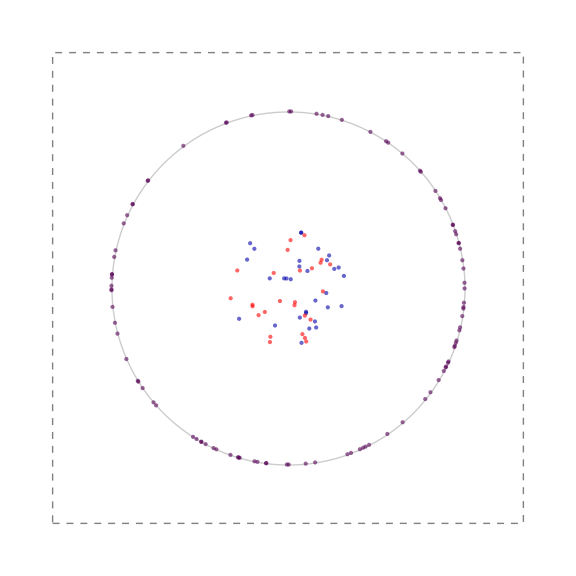

```mathematica
sim=With[{bounds = 0.25,numnodalparticles= 40, numleftyparticles=30,center = {0,0},cellradius  =0.75, numreceptors = 100,nSteps = 3000},

Module[{nodallist, nodalBoundaryindex, nodalpts,leftylist,leftyBoundaryindex,leftypts, membranepts,membraneindex,countnod,countleft,listprod={},temp,g,boundn,boundp},

(* we generate the initial configuration here *)

{nodallist,nodalBoundaryindex,nodalpts} = 
initialParticleConfig["nodal",{-bounds,bounds},numnodalparticles];
countnod = Length@nodalBoundaryindex;

{leftylist,leftyBoundaryindex,leftypts}=initialParticleConfig["lefty",{-bounds,bounds},numleftyparticles];
countleft = Length@leftyBoundaryindex;

{membranepts,membraneindex}=membraneReceptorConfig[center,cellradius,numreceptors];

(* printing the intial configuration *)
Print@Graphics[{{Gray,Dashed,Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}]},{Black,Opacity[0.2],Circle[center,cellradius]},{PointSize[Medium],Opacity[0.6],Darker@Purple,Point@membranepts},{Darker@Blue,PointSize[Medium],Opacity[0.6],Point@nodalpts},{Red,Opacity[0.6],PointSize[Medium],Point@leftypts}},ImageSize->Large];

Monitor[Reap[Nest[(temp=BrownianSimulation@@#;
boundn = Cases[temp[[5]],patt:PatternSequence[_->{{_,_},_,_,"nodal"}]:> patt[[2,1]],2];
boundp = Cases[temp[[5]],patt:PatternSequence[_->{{_,_},_,_,"lefty"}]:> patt[[2,1]],2];

Sow[{Length@boundn+Length@temp[[1]],Length@boundp+Length@temp[[3]]}];

g = graphState[temp[[5]],temp[[1]],temp[[3]],boundn,boundp];

temp[[1]] = Association@Map[#[[1]]->{"nodal",#[[3]]}&,temp[[1]]];
temp[[3]] = Association@Map[#[[1]]->{"lefty",#[[3]]}&,temp[[3]]];
temp)&,{nodallist,nodalBoundaryindex,leftylist,leftyBoundaryindex,membraneindex,membranepts,countnod,countleft,listprod},nSteps]],
g]//Quiet
]
];
```

## basic stats

```mathematica
{tracknodal,tracklefty}=Thread@Flatten[sim[[2]],1];
```

```mathematica
membraneindex=sim[[1,5]];
```

```mathematica
leftylist=sim[[1,3]];
```

```mathematica
nodallist = sim[[1,1]];
```

```mathematica
xnodal = Position[Differences@tracknodal,_?(#<0&)];
```

```mathematica
ynodal = tracknodal[[Flatten@xnodal]];
```

```mathematica
noddeathevents = Thread[{Flatten@xnodal,ynodal}]
```

{{2960,259}}

```mathematica
xlefty = Position[Differences@tracklefty,_?(#<0&)];
```

```mathematica
ylefty = tracklefty[[Flatten@xlefty]];
```

```mathematica
leftydeathevents = Thread[{Flatten@xlefty,ylefty}]
```

{{2410,163},{2577,180}}

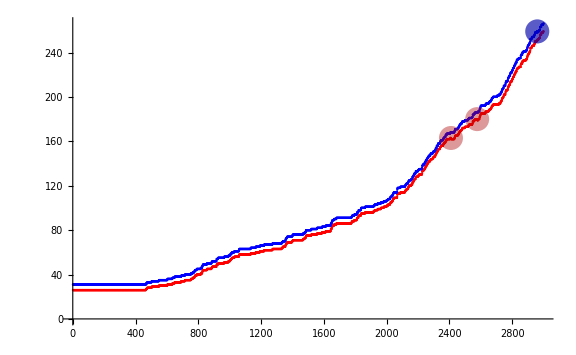

```mathematica
ListPlot[{tracklefty,tracknodal,leftydeathevents/.{}-> {None,None},noddeathevents/.{}-> {None,None}},PlotStyle->{Red,Blue,{Darker@Red,PointSize[0.03],Opacity[0.4]},{Darker@Blue,PointSize[0.03],Opacity[0.4]}},PlotRange->All, ImageSize->Large]
```

## (indices of dead particles)

```mathematica
Complement[Range[sim[[1,7]]],Join[nodallist//Keys,Cases[membraneindex,PatternSequence[_ -> {_,_,y_,"nodal"}]:> y]]]
```

{148}

```mathematica
Complement[Range[sim[[1,8]]],Join[leftylist//Keys,Cases[membraneindex,PatternSequence[_ -> {_,_,y_,"lefty"}]:> y]]]
```

{1,19,157}

```mathematica
ndead = sim[[1,7]]- (Sort@Join[nodallist//Keys,Cases[membraneindex,PatternSequence[_-> {_,_,_,"nodal"}]][[All,2,3]]]//Length) (* dead nodal *)
```

1

```mathematica
ldead = sim[[1,8]]-(Length@Sort@Join[leftylist//Keys,Cases[membraneindex,PatternSequence[_-> {_,_,_,"lefty"}]][[All,2,3]]]) (* dead lefty *)
```

3

## others

```mathematica
Differences@tracknodal//Cases[#,_?(Positive)]&//Total (* if a particle is produced and destroyed in the same iteration, then neither the production nor the death event gets recorded. For instance {a,(a existing particles +1 produced -1 destroyed) -> a}. The simulation is correct; only that there is currently no means to record death event explicitly. Always look at indices to determine how many particles died *)
```

236

```mathematica
Total@Cases[#,_?(Positive)]&@Differences@tracklefty
```

235

```mathematica
Differences@tracknodal//Counts
```

<|0→2774,1→212,2→12,-1→1|>

```mathematica
Differences@tracklefty//Counts
```

<|0→2774,1→211,2→12,-1→2|>

```mathematica
(sim[[1,7]]-tracknodal[[1]]) === (sim[[1,8]]-tracklefty[[1]])(* same production for nodal and lefty *)
```

True

```mathematica
tracknodal[[1]]-tracklefty[[1]]=== sim[[1,7]]-sim[[1,8]] (* constant index difference b/w nodal and lefty. same as above *)
```

True

```mathematica
tracknodal[[1]]-tracklefty[[1]]
```

5

```mathematica
sim[[1,7]]
```

267

```mathematica
sim[[1,8]]
```

262

```mathematica
Max@Join[nodallist//Keys,Cases[membraneindex,PatternSequence[_ -> {_,_,y_,"nodal"}]:> y]]
```

267

```mathematica
Max@Join[leftylist//Keys,Cases[membraneindex,PatternSequence[_ -> {_,_,y_,"lefty"}]:> y]]
```

262